## Логистическая регрессия и регуляризация.

##### Постановка задачи.

Задано множество объектов X  и существует множество ответов Y={0,1} -бинарное множество  и существует целевая функция y^*:X→Y, значения которой y_i=y^*(x_i) известны только на конечном подмножестве объектов {x_1,...,x_l}⊂X.

Требуется по заданному множеству пар объект-ответ восстановить классифицирующую функцию a(x):X→ Y.

Определим вид функции a(x):

a(x,θ)=(1-ⅇ^-θᵀx)^-1

Метод логистической регрессии имеет ряд особенностей, одна из которых - возникновение возможности на ряду с классификацией объекта получать численные оценки вероятности его принадлежности каждому из классов.

Значение функции a(x,θ) будем определять как вероятность принадлежности объекта x к классу y=1:

p(+1|x,θ)=a(x,θ),
 p(0|x,θ)=1-a(x,θ).

Тогда уравнение θᵀx=0 задает разделяющую поверхность между двумя классами.

Решение задачи классификации будем проводить методом минимизации эмпирического риска. Для этого определим функцию потерь:

Q(θ)=1/l∑_(i=1)^l (-y^(i)ln(a(x^(i),θ))-(1-y^(i))ln(1-a(x^(i),θ)))

Тогда для нахождения решающей функции a(x,θ), необходимо решить задачу оптимизации:

a(x,θ), где θ=arg min_θ Q(θ)

Дополнительно рассмотрим проблему переобучения.

Переобучение - явление, при котором решающая функция подстраивается под обучающую выборку настолько, что теряет способность обобщать и становится слишком уязвимой для шумов.

Для предотвращения переобучения можно ввести дополнительное ограничение размеры θ_i:

Q(θ,λ)=1/l∑_(i=1)^l (-y^(i)ln(a(x^(i),θ))-(1-y^(i))ln(1-a(x^(i),θ)))+λ/(2m)∑_(i=1)^n θ_i^2
a(x,θ), где θ=arg min_θ Q(θ,λ)

Примечание:

Условие малости не накладывается на коэффициент θ_0.

Рассмотрим пример:

##### Пример

Пусть у нас имеется обучающее множество объектов data:

```mathematica
data=Import["C:\\Users\\Я\\Desktop\\machine-learning-ex2\\ex2\\ex2data2.txt","Data"];
```

Объект data[[i]] имеет следующий вид:

```mathematica
data[[1]]
```

{0.051267,0.69956,1}

Где его первый элемент - это признак x_1, второй элемент - признак x_2, третий элемент - класс этого объекта.

Проиллюстрируем на плоскости распределение объектов. Для этого разделим множество data на X1 и X2, где Х1 - множество объектов первого класса,Х1 - множество объектов второго класса.

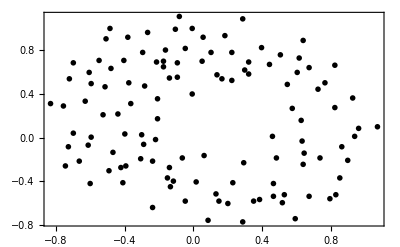

```mathematica
X1=Select[data,#[[3]]==0&][[;;,{1,2}]];
X2=Select[data,#[[3]]==1&][[;;,{1,2}]];
ListPlot[{X1,X2},PlotStyle->{PointSize[1]},Frame->True,ImageSize->400,Axes->False]
```

Из данной диаграммы видно, через обучающую выборку провести линейную границу невозможно. Следовательно необходимо введение дополнительных признаков x_1^2,x_1 x_2,... и т.д.

Составим комбинацию признаков x_1 и x_2 вплоть до шестой степени следующим образом:

```mathematica
x1x2=Flatten@{1,Table[#1^(i-j)*#2^j,{i,1,6},{j,0,i}]}&[x1,x2]
```

{1,x1,x2,x1^2,x1 x2,x2^2,x1^3,x1^2 x2,x1 x2^2,x2^3,x1^4,x1^3 x2,x1^2 x2^2,x1 x2^3,x2^4,x1^5,x1^4 x2,x1^3 x2^2,x1^2 x2^3,x1 x2^4,x2^5,x1^6,x1^5 x2,x1^4 x2^2,x1^3 x2^3,x1^2 x2^4,x1 x2^5,x2^6}

Данная комбинация признаков позволит нам задавать сложные разделяющие поверхности.

Отсортируем множество объектов data по их классу:

```mathematica
data=SortBy[data,Last];
```

Запишем множества X,Y - множество признаком объектов, множество классов объектов.

```mathematica
Y=data[[;;,{3}]];
X=Table[Flatten@{1,data[[i,{1,2}]]},{i,1,Length[data]}];
```

Теперь составим комбинацию каждого i_ого признака по образцу записанному выше:

```mathematica
XX=Table[Flatten@{1,Table[(data[[k]][[1]])^(i-j)*(data[[k]][[2]])^j,{i,1,6},{j,0,i}]},{k,1,Length[data]}];
```

Теперь зададим решающую функцию и функцию потерь:

```mathematica
a[x_,θ_]:=1/(1+Exp[-θ.x])
Q[θ_,λ_]:=1/(2Length[data])(Sum[-Y[[i]]Log[a[XX[[i]],θ]]-(1-Y[[i]])Log[1-a[XX[[i]],θ]],{i,1,Length[data]}]+λ  Sum[θ[[i]]^2,{i,2,Length[θ]}])
```

Получим решение с помощью функции численной оптимизации NArgMin:

```mathematica
θ[l_]:=NArgMin[Q[Table[x[i],{i,0,27}],l],Table[x[i],{i,0,27}],MaxIterations->1000,AccuracyGoal->4]
```

Случай когда θ=θ(0) соответствует отсутствию регуляризации. Построим разделяющую поверхность в этом случае:

```mathematica
θ[0]
```

{38.2303,55.5952,98.1459,-369.424,-177.116,-194.257,-366.004,-842.202,-719.442,-511.892,1182.68,1279.32,1907.87,914.303,514.274,573.215,1629.73,2553.58,2919.05,1780.6,785.313,-1257.89,-2259.97,-4142.74,-4290.54,-4229.61,-2055.53,-750.377}

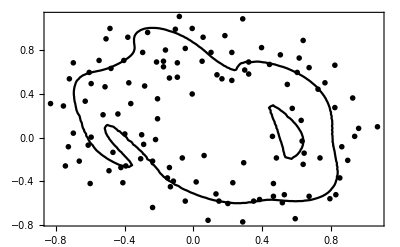

```mathematica
Show[ListPlot[{X1,X2},PlotStyle->{PointSize[Large]},Axes->False,Frame->True,ImageSize->400],ContourPlot[Evaluate[θ[0].x1x2==0],{x1,-2,2},{x2,-2,2}]]
```

Данный пример наглядно демонстрирует эффект переобучения: граница слишком волнистая, шумы создают вокруг себя дополнительные области. К счастью, как уже было сказано раннее, регуляризация устраняет данный недостаток логистической регрессии.

Рассмотрим 4 примера, в которых λ={0.01,0.1,1,10}:

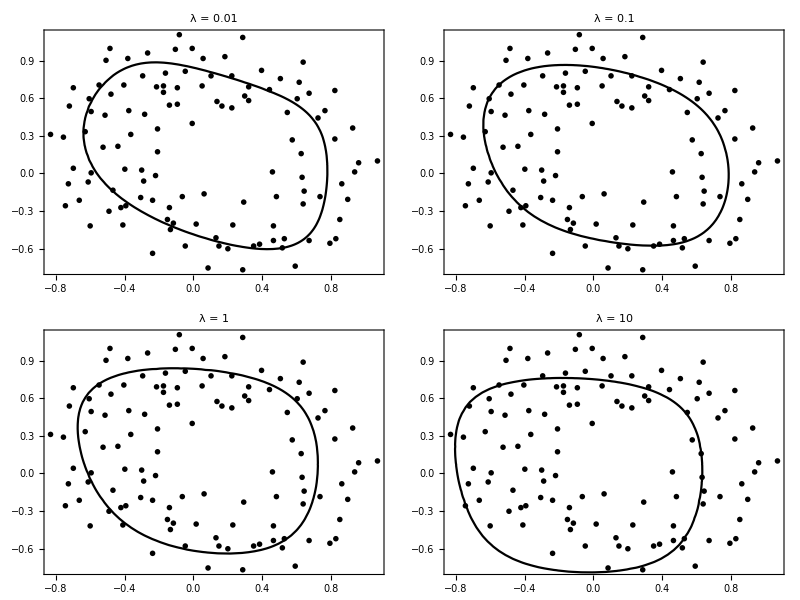

```mathematica
Grid@Partition[Table[Show[ListPlot[{X1,X2},PlotStyle->{PointSize[Large]},Axes->False,PlotLabel->StringJoin@{"λ = "  ,ToString@k},ImageSize->280,Frame->True],ContourPlot[Evaluate[θ[k].x1x2==0],{x1,-1,1},{x2,-1,1}]],{k,{0.01,0.1,1,10}}],2]
```

Как мы видим, введение коэффициента регуляризации позволяет избежать эффекта переобучения, но слишком большое его значение ведет к эффекту недообучения. Оптимальное его значение для данной задачи λ≈0.1.

Также, для наглядности, можем построить область, объекты в которой классифицируются полученным алгоритмом как класс 0:

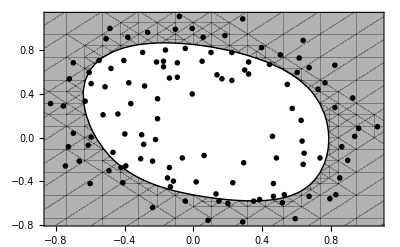

```mathematica
Show[ListPlot[{X1,X2},PlotStyle->{PointSize[Large]},Frame->True,Axes->False,ImageSize->400],RegionPlot[Evaluate[θ[0.1].x1x2<=0],{x1,-2,2},{x2,-2,2}]]
```